```mathematica
(* Comandi per convertire il notebook in codice latex, fonte: *)
(* https://mathematica.stackexchange.com/questions/73223/how-best-to-embed-various-cell-groups-into-a-latex-project/73589#73589 *)
(*
Import["https://raw.githubusercontent.com/jkuczm/\
MathematicaSyntaxAnnotations/master/SyntaxAnnotations/\
SyntaxAnnotations.m"]

Import["https://raw.githubusercontent.com/jkuczm/\
MathematicaCellsToTeX/master/NoInstall.m"]
*)
```

# Studio numerico della transizione di fase superradiante del modello di Dicke mediante l’approccio di Hopfield-Bogoliubov

## Diagonalizzazione numerica dell’Hamiltoniana luce-materia

## Sistema isolato

## Fase normale

```mathematica
(* Definizione della matrice di Hopfield-Bogoliouv nella fase normale *)
MNP[g_] := {
	{-I ω - κ, 0, -I g, -I g}, 
	{0, I ω - κ, I g, I g}, 
	{-I g, -I g, -I ω0, 0}, 
	{I g, I g, 0, I ω0}
};
```

```mathematica
(* Calcolo simbolico degli autovalori*)
Eigenvalues[MNP[g]] //MatrixForm
```

(Root[-4 g^2 ω ω0+κ^2 ω0^2+ω^2 ω0^2+2 κ ω0^2 #1+(κ^2+ω^2+ω0^2) #1^2+2 κ #1^3+#1^4&,1]
Root[-4 g^2 ω ω0+κ^2 ω0^2+ω^2 ω0^2+2 κ ω0^2 #1+(κ^2+ω^2+ω0^2) #1^2+2 κ #1^3+#1^4&,2]
Root[-4 g^2 ω ω0+κ^2 ω0^2+ω^2 ω0^2+2 κ ω0^2 #1+(κ^2+ω^2+ω0^2) #1^2+2 κ #1^3+#1^4&,3]
Root[-4 g^2 ω ω0+κ^2 ω0^2+ω^2 ω0^2+2 κ ω0^2 #1+(κ^2+ω^2+ω0^2) #1^2+2 κ #1^3+#1^4&,4])

```mathematica
(* Parametri numerici del modello isolato *)
parametersClosedModel = {ω -> 1., ω0 -> 1., κ -> 0};

(* Intervallo dei valori del parametro di accoppiamento g per la fase normale *)
gIntervalNP = Range[0.0, 0.5, 0.001];
```

```mathematica
(* Calcolo numerico degli autovalori*)
eigenvaluesTableNP = Table[
	Eigenvalues[MNP[g] /. parametersClosedModel], {g, gIntervalNP}
];
```

```mathematica
energyNP = Table[
	Abs[Eigenvalues[MNP[g] /. parametersClosedModel]], {g, gIntervalNP}
];
```

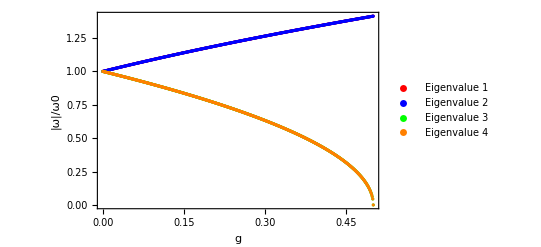

```mathematica
plotEigenvalues[data_,yLabel_,interval_]:=
	ListPlot[Transpose[{interval,#}]&/@Transpose[data],
	PlotStyle->{Red,Blue,Green,Orange},
	PlotLegends->{"Eigenvalue 1","Eigenvalue 2",
				 "Eigenvalue 3","Eigenvalue 4"},
	Frame->True,
	FrameLabel->{Style["g",18],Style[yLabel,18]},
	LabelStyle->Directive[16],
	TicksStyle->Directive[16]
];

(* Visualizzazione della relazione di dispersione *)
plotEigenvalues[energyNP, "|ω|/ω0", gIntervalNP]
```

```mathematica
(* Raggruppamento degli autovalori in coppie, ciascuna associata ad un modo normale *)
(* Il carattere fotonico e atomico vengono distinti in base al comportamento dei modi normali mostrati nel grafico della relazione di dispersione *)

(* Creazione struttura dati per rappresentare la relazione di dispersione *)
energyAtomicBranchNP = Join[
	Transpose[{gIntervalNP, energyNP[[All, 1]]}],
	Transpose[{gIntervalNP, energyNP[[All, 2]]}]
];
energyPhotonicBranchNP = Join[
	Transpose[{gIntervalNP, energyNP[[All, 3]]}],
	Transpose[{gIntervalNP, energyNP[[All, 4]]}]
];
```

## Fase superradiante

```mathematica
(* Definizione dei parametri e della matrice di Hopfield-Bogoliouv nella fase superradiante *)
gc = 1/2 Sqrt[(ω0/ω) * (κ*κ + ω*ω)];
μ = gc/g;
ω0tilde = ( ω0/(2 μ) ) * (1+μ);
d = ( ω0 * (1-μ) * (3+μ) ) / ( 8 * μ * (1+μ) );
gtilde = g * μ Sqrt[2/(1+μ)];

MSP[g_] := {
	{-I ω - κ, 0, -I gtilde, -I gtilde}, 
	{0, I ω - κ, I gtilde, I gtilde}, 
	{-I gtilde, -I gtilde, -I(ω0tilde + d), -I 2d}, 
	{I gtilde, I gtilde, I 2d, I(ω0tilde + d)}
};

(* Calcolo simbolico degli autovalori*)
Eigenvalues[MSP[g]] //MatrixForm;
```

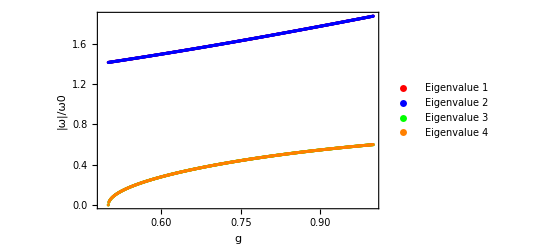

```mathematica
(* Intervallo dei valori del parametro di accoppiamento g per la fase superradiante*)
gIntervalSP = Range[0.5, 1.0, 0.001];

(* Calcolo numerico degli autovalori*)
eigenvaluesTableSP = Table[
	Eigenvalues[MSP[g] /. parametersClosedModel], 
{g, gIntervalSP}
]; 

(* Visualizzazione dei quattro autovalori della lista *)
eigenvaluesTableSP //Chop // MatrixForm;

(* Calcolo e visualizzazione della relazione di dispersione *)
energySP = Table[
	Abs[Eigenvalues[MSP[g] /. parametersClosedModel]], 
{g, gIntervalSP}
];

plotEigenvalues[energySP, "|ω|/ω0", gIntervalSP]
```

```mathematica
(* Raggruppamento degli autovalori in coppie, ciascuna associata ad un modo normale *)
(* Il carattere fotonico e atomico vengono distinti in base al comportamento dei modi normali mostrati nel grafico della relazione di dispersione *)

energyAtomicBranchSP = Join[
	Transpose[{gIntervalSP, energySP[[All, 1]]}],
	Transpose[{gIntervalSP, energySP[[All, 2]]}]
];
energyPhotonicBranchSP = Join[ 
	Transpose[{gIntervalSP, energySP[[All, 3]]}],
	Transpose[{gIntervalSP, energySP[[All, 4]]}]
];
```

## Spettro energetico

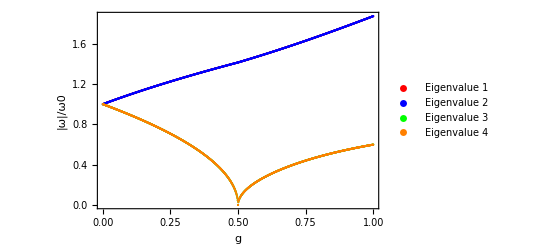

```mathematica
(* Unione dei dati NP e SP di tutti e quattro gli aurovalori *)
eigenvaluesCurves = Table[Join[
	Transpose[{gIntervalNP, energyNP[[All, i]]}],
	Transpose[{gIntervalSP, energySP[[All, i]]}]
	],{i, 1, 4}
];

(* Grafico che mostra il ruolo degli autovalori ai fini del modo collettivo *)
ListPlot[eigenvaluesCurves,
	PlotRange -> All,
	PlotStyle -> {Red, Blue, Green, Orange},
	PlotLegends -> {"Eigenvalue 1", "Eigenvalue 2",
				   "Eigenvalue 3", "Eigenvalue 4"},
	AxesLabel -> {"g", "|ω|/ω0"},
	Frame->True,
	FrameLabel->{Style["g",18],Style["|ω|/ω0",18]},
	LabelStyle->Directive[16],
	TicksStyle->Directive[16]
]
```

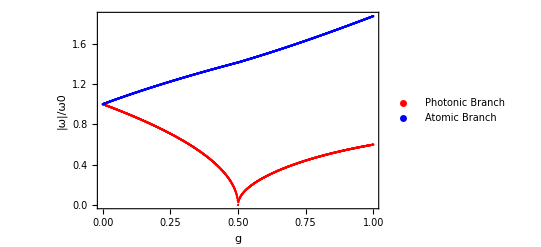

```mathematica
(* Grafico che mostra i due modi collettivi *)
ListPlot[
	{
	 Join[energyPhotonicBranchNP, energyPhotonicBranchSP],
	 Join[energyAtomicBranchNP, energyAtomicBranchSP]
	},
	PlotRange -> All,
	PlotStyle -> {Red, Blue},  
    PlotLegends -> {"Photonic Branch", "Atomic Branch"},
    AxesLabel -> {"λ", "|ω|/ω0"},
	Frame->True,
	FrameLabel->{Style["g",18],Style["|ω|/ω0",18]},
	LabelStyle->Directive[16],
	TicksStyle->Directive[16]
]
```

## Sistema aperto

## Fase normale

```mathematica
(* Parametri numerici del modello aperto *)
parametersOpenModel   = {ω -> 1., ω0 -> 1., κ -> 0.2};
```

```mathematica
(* Calcolo numerico degli autovalori*)
eigenvaluesTableNP = Table[
	Eigenvalues[MNP[g] /. parametersOpenModel], {g, gIntervalNP}
];
```

```mathematica
(* Raggruppamento degli autovalori in coppie, ciascuna associata ad un modo normale *)
(* Il carattere fotonico e atomico vengono distinti in base al comportamento dei modi normali mostrati nel grafico della relazione di dispersione *)

(* Estrazione delle parti reale e immaginaria per i modi atomici e fotonici *)
realAtomicBranchNP = Join[
	Transpose[{gIntervalNP, Re[eigenvaluesTableNP[[All, 1]]]}],
	Transpose[{gIntervalNP, Re[eigenvaluesTableNP[[All, 2]]]}]
];
imagAtomicBranchNP = Join[
	Transpose[{gIntervalNP, Im[eigenvaluesTableNP[[All, 1]]]}],
	Transpose[{gIntervalNP, Im[eigenvaluesTableNP[[All, 2]]]}]
];
realPhotonicBranchNP = Join[
	Transpose[{gIntervalNP, Re[eigenvaluesTableNP[[All, 3]]]}],
	Transpose[{gIntervalNP, Re[eigenvaluesTableNP[[All, 4]]]}]
];
imagPhotonicBranchNP = Join[
	Transpose[{gIntervalNP, Im[eigenvaluesTableNP[[All, 3]]]}],
	Transpose[{gIntervalNP, Im[eigenvaluesTableNP[[All, 4]]]}]
];

(* Creazione struttura dati per rappresentare la relazione di dispersione *)
energyAtomicBranchNP = Join[
	Transpose[{gIntervalNP, Abs[eigenvaluesTableNP[[All, 1]]]}],
	Transpose[{gIntervalNP, Abs[eigenvaluesTableNP[[All, 2]]]}]
];
energyPhotonicBranchNP = Join[
	Transpose[{gIntervalNP, Abs[eigenvaluesTableNP[[All, 3]]]}],
	Transpose[{gIntervalNP, Abs[eigenvaluesTableNP[[All, 4]]]}]
];
```

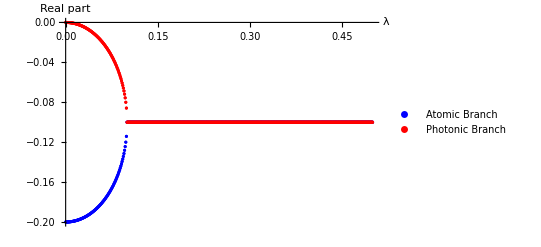

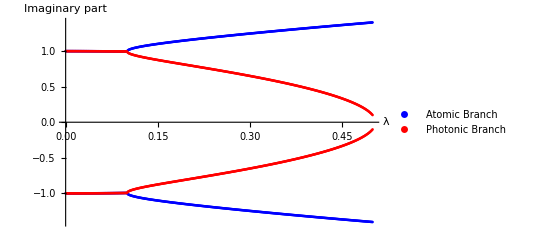

```mathematica
(* Funzione che genera il ListPlot per le branche atomiche e fotoniche *)
plotBranches[atomicBranch_, photonicBranch_, yLabel_] :=  
	ListPlot[{atomicBranch, photonicBranch},
		PlotRange -> All,
		PlotStyle -> {Blue, Red},
        PlotLegends -> {"Atomic Branch", "Photonic Branch"},
        AxesLabel -> {"λ", yLabel}
];

(* Visualizzazione della parte reale e immaginaria dei due modi normali *)
plotBranches[realAtomicBranchNP, realPhotonicBranchNP, "Real part"]
plotBranches[imagAtomicBranchNP, imagPhotonicBranchNP, "Imaginary part"]
```

## Fase superradiante

```mathematica
(* Calcolo numerico degli autovalori*)
eigenvaluesTableSP = Table[
	Eigenvalues[MSP[g] /. parametersOpenModel], {g, gIntervalSP}
]; 

(* Raggruppamento degli autovalori in coppie, ciascuna associata ad un modo normale *)
(* Il carattere fotonico e atomico vengono distinti in base al comportamento dei modi normali mostrati nel grafico della relazione di dispersione *)

(* Estrazione delle parti reale e immaginaria per i modi atomici e fotonici *)
realAtomicBranchSP = Join[
	Transpose[{gIntervalSP, Re[eigenvaluesTableSP[[All, 1]]]}],
	Transpose[{gIntervalSP, Re[eigenvaluesTableSP[[All, 2]]]}]
];
imagAtomicBranchSP = Join[
	Transpose[{gIntervalSP, Im[eigenvaluesTableSP[[All, 1]]]}],
	Transpose[{gIntervalSP, Im[eigenvaluesTableSP[[All, 2]]]}]
];
realPhotonicBranchSP = Join[
	Transpose[{gIntervalSP, Re[eigenvaluesTableSP[[All, 3]]]}],
	Transpose[{gIntervalSP, Re[eigenvaluesTableSP[[All, 4]]]}]
];
imagPhotonicBranchSP = Join[
	Transpose[{gIntervalSP, Im[eigenvaluesTableSP[[All, 3]]]}],
	Transpose[{gIntervalSP, Im[eigenvaluesTableSP[[All, 4]]]}]
];

(* Creazione struttura dati per rappresentare la relazione di dispersione *)
energyAtomicBranchSP = Join[
	Transpose[{gIntervalSP, Abs[eigenvaluesTableSP[[All, 1]]]}],
	Transpose[{gIntervalSP, Abs[eigenvaluesTableSP[[All, 2]]]}]
];
energyPhotonicBranchSP = Join[ 
	Transpose[{gIntervalSP, Abs[eigenvaluesTableSP[[All, 3]]]}],
	Transpose[{gIntervalSP, Abs[eigenvaluesTableSP[[All, 4]]]}]
];
```

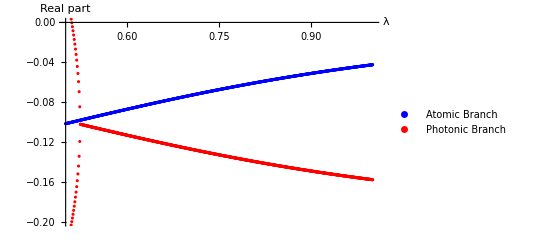

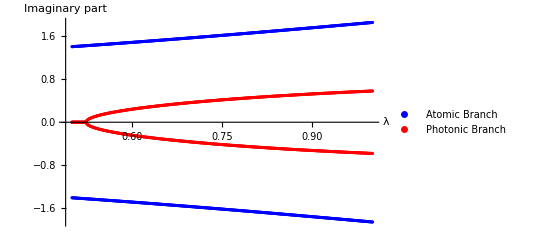

```mathematica
(* Visualizzazione della parte reale e immaginaria dei due modi normali *)
ListPlot[{realAtomicBranchSP, realPhotonicBranchSP},
	PlotRange -> {{0.5, 1.0},{0.0, -0.2}},
	PlotStyle -> {Blue, Red},
	PlotLegends -> {"Atomic Branch", "Photonic Branch"},
	AxesLabel -> {"λ", "Real part"}
]
plotBranches[imagAtomicBranchSP, imagPhotonicBranchSP, "Imaginary part"]
```

## Sinolo di materia e forma (luce)

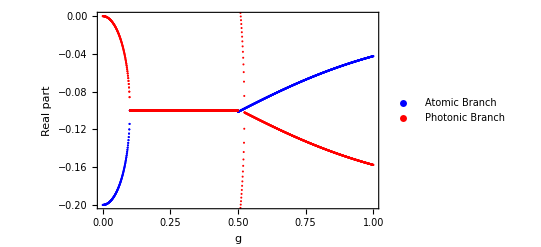

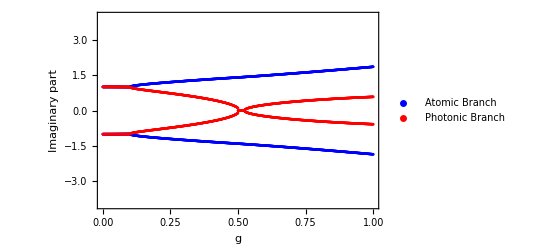

```mathematica
(* Visualizzazione per la parte reale *)
ListPlot[
	{
	 Join[realAtomicBranchNP, realAtomicBranchSP],
	 Join[realPhotonicBranchNP, realPhotonicBranchSP]
	},
	PlotRange -> {{0.0, 1.0},{0.0, -0.2}},
	PlotStyle -> {Blue, Red},
	PlotLegends -> {"Atomic Branch", "Photonic Branch"},
	Frame->True,
	FrameLabel->{Style["g",18],Style["Real part",18]},
	LabelStyle->Directive[16],
	TicksStyle->Directive[16]
]

(* Visualizzazione per la parte immaginaria *)
ListPlot[
	{
	 Join[imagAtomicBranchNP, imagAtomicBranchSP],
	Join[imagPhotonicBranchNP, imagPhotonicBranchSP]
	},
	PlotRange -> {{0.0, 1.0},{-4.0, 4.0}},
	PlotStyle -> {Blue, Red},  
	PlotLegends -> {"Atomic Branch", "Photonic Branch"},
	Frame->True,
	FrameLabel->{Style["g",18],Style["Imaginary part",18]},
	LabelStyle->Directive[16],
	TicksStyle->Directive[16]
]
```

## Spettro energetico

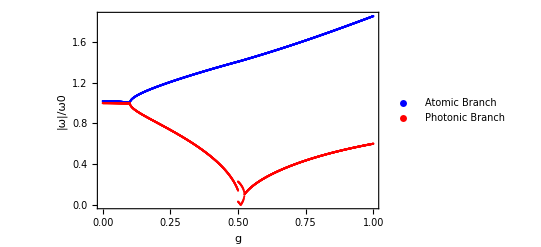

```mathematica
ListPlot[
	{
	 Join[energyAtomicBranchNP, energyAtomicBranchSP],
	 Join[energyPhotonicBranchNP, energyPhotonicBranchSP]
	},
	PlotRange -> All,
	PlotStyle -> {Blue, Red},
	PlotLegends -> {"Atomic Branch", "Photonic Branch"},
	AxesLabel -> {"λ", "|ω|/ω0"},
	Frame->True,
	FrameLabel->{Style["g",18],Style[ "|ω|/ω0",18]},
	LabelStyle->Directive[16],
	TicksStyle->Directive[16]
	]
```

```mathematica
(* Comandi per convertire il notebook in codice latex, fonte: *)
(* https://mathematica.stackexchange.com/questions/73223/how-best-to-embed-various-cell-groups-into-a-latex-project/73589#73589 *)
(*
SetOptions[CellToTeX, "CurrentCellIndex" -> Automatic];
ExportString[
 NotebookGet[] /. 
  cell : Cell[_, __] :> Cell[CellToTeX[cell], "Final"], "TeX", 
 "FullDocument" -> False, "ConversionRules" -> {"Final" -> Identity}]
*)
```